```mathematica
{inrad,outrad}={1/20 √(250+110 √5),1/4 (√3+√15)};
rescalef[r_]:=Re[1/2 (ArcSin[2 r-1]+π/2)];
coef1=0.01;
coef2=1.*^-5;
rescalef1[r_]:=coef1+(1-coef1)rescalef[(1-coef2)(r-inrad)/(outrad-inrad)+coef2/2];
```

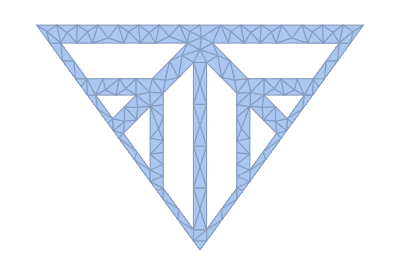
```mathematica
triangle2D=-Graphics-;
```

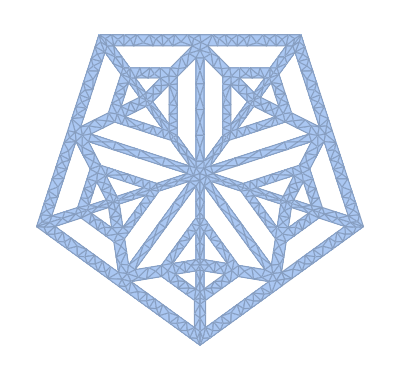

```mathematica
coords2D=Transpose[{#[[;;,1]],#[[;;,2]]-Min[#[[;;,2]]]}]&@MeshCoordinates@triangle2D;
pentagon2D=MeshRegion[Module[{a={}},Do[a~AppendTo~RotationTransform[i Degree][coords2D],{i,0,288,72}];Catenate@a],Module[{a={}},Do[a~AppendTo~(Polygon@@@(List@@@MeshCells[triangle2D,2]+i*Length@coords2D)),{i,0,4}];Catenate@a]]
```

```mathematica
x=MeshCoordinates[pentagon2D];
n=Length[x];
x=Join[x,ConstantArray[-1/20 √(250+110 √5),{n,1}],2];
t=0.05;
y=t ConstantArray[{0,0,0},n]+(1-t) x;
triangles=MeshCells[pentagon2D,2,"Multicells"->True][[1,1]];
prisms=Join[triangles,triangles+n,2];
pentagon3D=MeshRegion[Join[x,y],Prism[prisms]]
```

-Graphics3D-

```mathematica
vertice=PolyhedronData["Dodecahedron","GraphicsComplex"][[1]]//N;
face=PolyhedronData["Dodecahedron","GraphicsComplex"][[2,1]];
center=Mean/@(face/.Association@@Rule@@@Riffle[Range@20,vertice]~Partition~2);
spin=RotationTransform[{{0,0,-1},#}]&/@center//Quiet;
spin[[9]]=TransformationFunction[({{-1., 0., 0., 0.}, {0., 1., 0., 0.}, {0., 0., 1., 0.}, {0., 0., 0., 1.}})];
```

```mathematica
full3D=MeshRegion[Module[{a={}},a~AppendTo~#[RotationTransform[54Degree,{0,0,1}][MeshCoordinates[pentagon3D]]]&/@spin;Catenate@a],Module[{a={},b=MeshCells[pentagon3D,2],c=MeshCoordinates[pentagon3D]},Do[a~AppendTo~(Polygon@@@(List@@@b+i*Length@c)),{i,0,11}];Catenate@a]]
```

-Graphics3D-

```mathematica
hyperfull3D=MeshRegion[80rescalef1[Norm@#]Normalize@#&/@MeshCoordinates[full3D],MeshCells[full3D,2]]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"Mathematica12_Spikey.stl",hyperfull3D]
```

D:\notebook\Spikey\Mathematica12_Spikey.stl

```mathematica
Needs["POVRayRender`"]
```